```mathematica
(* Define the sample space and probabilities *)
sampleSpace=Import["square_names_1.txt", "list"]
probabilities=Import["square_percentages_1.txt", "list"]
```

{Go,Mediterranean Avenue,Community Chest 1,Baltic Avenue,Income Tax,Reading Railroad,Oriental Avenue,Chance 1,Vermont Avenue,Connecticut Avenue,Jail / Just Visiting,St. Charles Place,Electric Company,States Avenue,Virginia Avenue,Pennsylvania Railroad,St. James Place,Community Chest 2,Tennessee Avenue,New York Avenue,Free Parking,Kentucky Avenue,Chance 2,Indiana Avenue,Illinois Avenue,B. & O. Railroad,Atlantic Avenue,Ventnor Avenue,Water Works,Marvin Gardens,Go to Jail,Pacific Avenue,North Carolina Avenue,Community Chest 3,Pennsylvania Avenue,Short Line,Chance 3,Park Place,Luxury Tax,Boardwalk}

{0.024391,0.0244577,0.0246284,0.0248225,0.0250736,0.0254185,0.0256284,0.0258721,0.02582,0.0256523,0.0254799,0.0254357,0.0252639,0.0251623,0.0252916,0.0254156,0.0253172,0.0251944,0.025208,0.0250772,0.0251222,0.0250546,0.0250306,0.0250633,0.024979,0.0249301,0.0249631,0.024835,0.0248424,0.0247889,0.0247474,0.0245836,0.0247221,0.0246985,0.0244894,0.0247083,0.024509,0.0245188,0.024346,0.0244574}

```mathematica
(*top five names and probs*)
topfivenames={}
topfiveprobs={}
max=First[First[Position[probabilities,Max[probabilities]]]]
topfivenames=Append[topfivenames,Part[sampleSpace,max]]
topfiveprobs=Append[topfiveprobs,Part[probabilities,max]]
probabilities=Delete[probabilities,max];
sampleSpace=Delete[sampleSpace,max];

max=First[First[Position[probabilities,Max[probabilities]]]]
topfivenames=Append[topfivenames,Part[sampleSpace,max]]
topfiveprobs=Append[topfiveprobs,Part[probabilities,max]]
probabilities=Delete[probabilities,max];
sampleSpace=Delete[sampleSpace,max];

max=First[First[Position[probabilities,Max[probabilities]]]]
topfivenames=Append[topfivenames,Part[sampleSpace,max]]
topfiveprobs=Append[topfiveprobs,Part[probabilities,max]]
probabilities=Delete[probabilities,max];
sampleSpace=Delete[sampleSpace,max];

max=First[First[Position[probabilities,Max[probabilities]]]]
topfivenames=Append[topfivenames,Part[sampleSpace,max]]
topfiveprobs=Append[topfiveprobs,Part[probabilities,max]]
probabilities=Delete[probabilities,max];
sampleSpace=Delete[sampleSpace,max];

max=First[First[Position[probabilities,Max[probabilities]]]]
(*topfive=Append[topfive,{Part[sampleSpace,max], Part[probabilities, max]}];*)
topfivenames=Append[topfivenames,Part[sampleSpace,max]]
topfiveprobs=Append[topfiveprobs,Part[probabilities,max]]
probabilities=Delete[probabilities,max];
sampleSpace=Delete[sampleSpace,max];

(*bottom five names and probs*)
bottomfivenames={}
bottomfiveprobs={}
min=First[First[Position[probabilities,Min[probabilities]]]]
bottomfivenames=Append[bottomfivenames,Part[sampleSpace,min]]
bottomfiveprobs=Append[bottomfiveprobs,Part[probabilities,min]]
probabilities=Delete[probabilities,min];
sampleSpace=Delete[sampleSpace,min];

min=First[First[Position[probabilities,Min[probabilities]]]]
bottomfivenames=Append[bottomfivenames,Part[sampleSpace,min]]
bottomfiveprobs=Append[bottomfiveprobs,Part[probabilities,min]]
probabilities=Delete[probabilities,min];
sampleSpace=Delete[sampleSpace,min];

min=First[First[Position[probabilities,Min[probabilities]]]]
bottomfivenames=Append[bottomfivenames,Part[sampleSpace,min]]
bottomfiveprobs=Append[bottomfiveprobs,Part[probabilities,min]]
probabilities=Delete[probabilities,min];
sampleSpace=Delete[sampleSpace,min];

min=First[First[Position[probabilities,Min[probabilities]]]]
bottomfivenames=Append[bottomfivenames,Part[sampleSpace,min]]
bottomfiveprobs=Append[bottomfiveprobs,Part[probabilities,min]]
probabilities=Delete[probabilities,min];
sampleSpace=Delete[sampleSpace,min];

min=First[First[Position[probabilities,Min[probabilities]]]]
bottomfivenames=Append[bottomfivenames,Part[sampleSpace,min]]
bottomfiveprobs=Append[bottomfiveprobs,Part[probabilities,min]]
probabilities=Delete[probabilities,min];
sampleSpace=Delete[sampleSpace,min];

bottomfivenames = Reverse[bottomfivenames]
bottomfiveprobs = Reverse[bottomfiveprobs]
```

{}

{}

8

{Chance 1}

{0.0258721}

8

{Chance 1,Vermont Avenue}

{0.0258721,0.02582}

8

{Chance 1,Vermont Avenue,Connecticut Avenue}

{0.0258721,0.02582,0.0256523}

7

{Chance 1,Vermont Avenue,Connecticut Avenue,Oriental Avenue}

{0.0258721,0.02582,0.0256523,0.0256284}

7

{Chance 1,Vermont Avenue,Connecticut Avenue,Oriental Avenue,Jail / Just Visiting}

{0.0258721,0.02582,0.0256523,0.0256284,0.0254799}

{}

{}

34

{Luxury Tax}

{0.024346}

1

{Luxury Tax,Go}

{0.024346,0.024391}

33

{Luxury Tax,Go,Boardwalk}

{0.024346,0.024391,0.0244574}

1

{Luxury Tax,Go,Boardwalk,Mediterranean Avenue}

{0.024346,0.024391,0.0244574,0.0244577}

28

{Luxury Tax,Go,Boardwalk,Mediterranean Avenue,Pennsylvania Avenue}

{0.024346,0.024391,0.0244574,0.0244577,0.0244894}

{Pennsylvania Avenue,Mediterranean Avenue,Boardwalk,Go,Luxury Tax}

{0.0244894,0.0244577,0.0244574,0.024391,0.024346}

{}

0

Delete::psl: Position specification 8 Chance 1 in {0.024391,0.0244577,0.0246284,0.0248225,0.0250736,0.0254185,0.0256284,0.0258721,0.02582,0.0256523,«30»} is not a machine-sized integer or a list of machine-sized integers.

Delete::psl: Position specification 8 Chance 1 in {Go,Mediterranean Avenue,Community Chest 1,Baltic Avenue,Income Tax,Reading Railroad,Oriental Avenue,Chance 1,Vermont Avenue,Connecticut Avenue,«30»} is not a machine-sized integer or a list of machine-sized integers.

Part::pkspec1: The expression {{8 Chance 1,0.206977}} cannot be used as a part specification.

Delete::psl: Position specification 8 {Go,Mediterranean Avenue,Community Chest 1,Baltic Avenue,Income Tax,Reading Railroad,Oriental Avenue,Chance 1,Vermont Avenue,Connecticut Avenue,«30»}⟦{{8 Chance 1,0.206977}}⟧ in {0.024391,0.0244577,0.0246284,0.0248225,0.0250736,0.0254185,0.0256284,0.0258721,0.02582,0.0256523,«30»} is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Delete::psl will be suppressed during this calculation.

Part::pkspec1: The expression {{8 {Go,Mediterranean Avenue,Community Chest 1,Baltic Avenue,Income Tax,Reading Railroad,Oriental Avenue,Chance 1,Vermont Avenue,Connecticut Avenue,«30»}⟦{{8 Chance 1,0.206977}}⟧,8 {0.024391,0.0244577,0.0246284,0.0248225,«4»,0.02582,0.0256523,«30»}⟦{«1»}⟧}} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

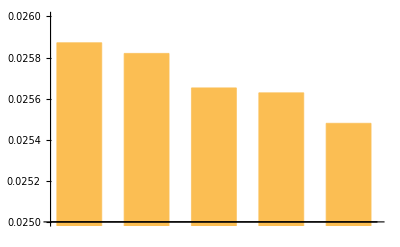

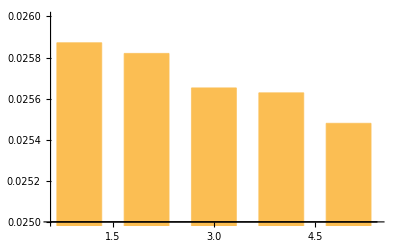

```mathematica
ch =
 BarChart[topfiveprobs,
  BarSpacing -> Large,
  PlotRange -> {Automatic, {0.025, 0.026}},
  PlotRangePadding -> {Automatic, 0},
  PlotRangeClipping -> True,
  ChartLabels -> Placed[topfivenames, Below, Rotate[#, 80 Degree] &]
 ]
 labels = Cases[ch[[1]], Text[lbl_, Offset[_, {pos_, _}], ___] :> {pos, lbl, 0}, -4];
 Show[ch, Ticks -> {labels}, Axes -> True]
```

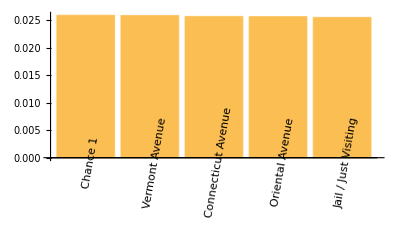

```mathematica
(*BarChart[topfiveprobs, ChartLabels ->Placed[topfivenames, Below, Rotate[#, 80 Degree] &],PlotRangePadding -> Automatic]*)
```

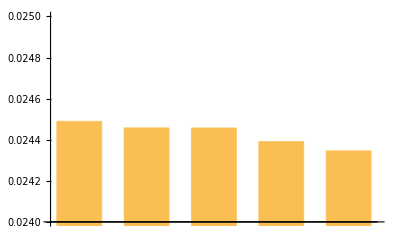

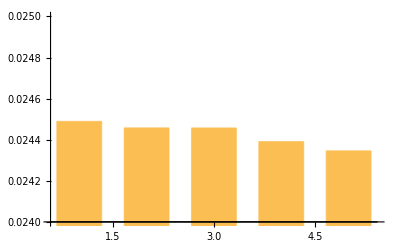

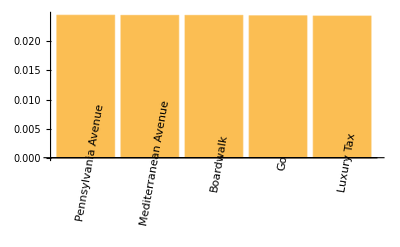

```mathematica
ch =
 BarChart[bottomfiveprobs,
  BarSpacing -> Large,
  PlotRange -> {Automatic, {0.024, 0.025}},
  PlotRangePadding -> {Automatic, 0},
  PlotRangeClipping -> True,
  ChartLabels -> Placed[bottomfivenames, Below, Rotate[#, 80 Degree] &]
 ]
 labels = Cases[ch[[1]], Text[lbl_, Offset[_, {pos_, _}], ___] :> {pos, lbl, 0}, -4];
 Show[ch, Ticks -> {labels}, Axes -> True]
BarChart[bottomfiveprobs, ChartLabels ->Placed[bottomfivenames, Below, Rotate[#, 80 Degree] &]]
```

```mathematica
bottomfivenames
```

{Pennsylvania Avenue,Mediterranean Avenue,Boardwalk,Go,Luxury Tax}

```mathematica
bottomfiveprobs
```

{0.0244894,0.0244577,0.0244574,0.024391,0.024346}

```mathematica
topfiveprobs
```

{0.0258721,0.02582,0.0256523,0.0256284,0.0254799}